# Mass Excess study

## Comparison between the last published mass excess study and the data inside Mathematica (Wolfram Language)

Made by Estevao Teixeira (estevao (at) ita.br)

You can also check this study at https://community.wolfram.com/groups/-/m/t/1766141?p_p_auth=iWGNgeT8

## Importing the data

Here we import the data from the mass16.dat file. First, we set the notebook directory and then we import it.

```mathematica
SetDirectory@NotebookDirectory[];
rawData = Import["mass16.dat","Lines"][[40;;]];
```

## Parsing the data file to a dataset

Using the format defined by the article authors, we now how to work in each line of the file. Let’s parse the file to a dataset.

```mathematica
parsedData = Map[
<|
"CC"-> StringTake[#,{1,1}],
"NZ"-> StringTake[#,{2,4}],
"N"-> StringTake[#,{5,9}],
"Z"-> StringTake[#,{10,14}],
"A"-> StringTake[#,{15,19}],
"El"-> StringTake[#,{21,23}],
"o"-> StringTake[#,{24,27}],
"mass"-> StringTake[#,{29,41}],
"masserror"-> StringTake[#,{42,52}],
"binding"-> StringTake[#,{53,63}],
"bindingerror"-> StringTake[#,{64,72}],
"B"-> StringTake[#,{74,75}],
"beta"-> StringTake[#,{76,87}],
"betaerror"-> StringTake[#,{88,96}],
"atomicmass"-> StringTake[#,{97,100}],
"atomicmassu"-> StringTake[#,{101,113}],
"atomicmasserror"-> StringTake[#,{114,UpTo[124]}]
|> &
,rawData]//Dataset;
```

```mathematica
parsedData
```

Dataset[<>]

## Data cleaning

In the previous step, we got all the information from the file. Now, we have to clean it and make it searchable.

## Cleaning whitespaces

We remove all whitespaces in every fields.

```mathematica
cleanData = Map[Map[If[StringLength[x=StringReplace[#,Whitespace-> ""]]<1,Missing[],x] &,#]&,parsedData];
```

## Defining helper functions

These functions will help us in the cleaning process. For example, in the data, the authors defined the character “*” to represent a “non-experimental” value. We will find these characters and fix other values.

The “clearNonExperimentalSign” removes “#” or “*” from a string.

```mathematica
clearNonExperimentalSign[s_String] := StringReplace[s,("#"|"*")-> ""];
```

The “clearNotMissing” parses all the info that are not missing

```mathematica
clearNotMissing[v_,unit_String,fixvalue_] := If[MissingQ@v,v,valueToQuantity[clearNonExperimentalSign@v,unit,fixvalue]];
```

The “matchNonExperimentalSign” finds all “#” characters and return if it is a “non-experimental” or “experimental” value.

```mathematica
matchNonExperimentalSign[s_String] :=  If[StringMatchQ[s,___~~"#"~~___],"non-experimental","experimental"];
```

And finally, the “valueToQuantity” transform any possible value to a WL Quantity.

```mathematica
valueToQuantity[s_,unit_String,fixvalue_] := If[NumberQ[ToExpression@s ],N@Quantity[ToExpression@s* fixvalue,unit],s];
```

## Final and parsed dataset

Now, we parse all the previous data to a final dataset with all the information parsed.

```mathematica
finalData = Map[
   <|
     "Mass List" -> <|
        "Element" -> Quiet[IsotopeData[{ToExpression@#[["Z"]], ToExpression@#[["A"]]}]] /. _IsotopeData -> #[["El"]] <> #[["A"]],
       "Origin" -> #[["o"]],
       "Mass" -> <|
          "value" -> valueToQuantity[clearNonExperimentalSign@#[["mass"]], "MeV", 10^-3],
         "error" -> valueToQuantity[clearNonExperimentalSign@#[["masserror"]], "MeV", 10^-3],
          "type" -> matchNonExperimentalSign@#[["mass"]]
         |>,
       "Binding" -> 
        <|
         "value" -> valueToQuantity[clearNonExperimentalSign@#[["binding"]], "MeV", 10^-3],
         "error" -> valueToQuantity[clearNonExperimentalSign@#[["bindingerror"]], "MeV", 10^-3],
         "type" -> matchNonExperimentalSign@#[["binding"]]
         |>,
       "BetaDecay" ->
        <|
         "type" -> #[["B"]],
         "value" -> clearNotMissing[#[["beta"]], "MeV", 10^-3],
         "error" -> clearNotMissing[#[["betaerror"]], "MeV", 10^-3]
         |>,
       "AtomicMass" -> 
        <|
         "A" -> #[["atomicmass"]],
         "N" -> #[["N"]],
         "Z" -> #[["Z"]],
         "value" -> valueToQuantity[clearNonExperimentalSign@#[["atomicmassu"]], "u", 10^-6],
         "error" -> valueToQuantity[clearNonExperimentalSign@#[["atomicmasserror"]], "u", 10^-6],
         "type" -> matchNonExperimentalSign@#[["atomicmassu"]]
         |>
       |> 
     |>
    &, cleanData
   ];
   
   finalData
```

Dataset[<>]

## Comparisons

## Adjusting our dataset

The final dataset is good but it contains a lot of information that we will not need in our comparisons. Let’s make it smaller. We just want the Element name, the mass and atomic mass information.

```mathematica
ReducedData = finalData[All,1,{"Element","Mass","AtomicMass"}]
```

Dataset[<>]

To plot, we need still less information. Because of that, we create the following variable

```mathematica
ExampleListToPlot = {#Element,ToExpression@#AtomicMass[["N"]],#Mass[["value"]]}&/@ReducedData[[2;;]]
```

Dataset[<>]

## Missing Isotopes in WL

As our data is the most recent one, we have to filter the information that are not in WL.

```mathematica
MissingElmentsInWL = Query[Select[StringQ[#["Element"]] &]] @ ReducedData[2;;]
```

Dataset[<>]

To plot, we will get just the Element name, neutron number (N) and the value of the Mass

```mathematica
ListMissingElementsWL ={#Element,ToExpression@#AtomicMass[["N"]],#Mass[["value"]]}&/@MissingElmentsInWL
```

Dataset[<>]

## Mass excess plot by neutron number

We have the list with all elements and the missing elements. We plot it differentiating the missing ones as the red dots.

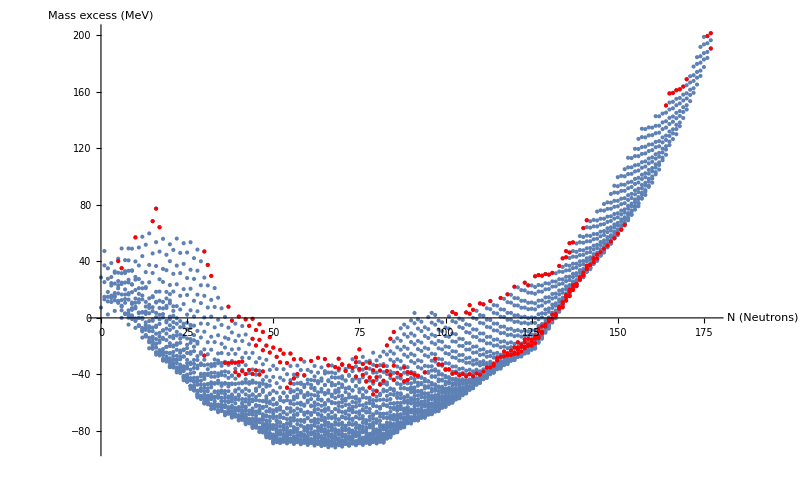

```mathematica
ListPlot[{ExampleListToPlot[[All,{2,3}]],ListMissingElementsWL[[All,{2,3}]]},PlotRange->All,PlotStyle->{{},{Red}}, AxesLabel->{"N (Neutrons)","Mass excess (MeV)"}]
```

## WL Mass Excess

We know that Mathematica (WL) has a lot of information about isotopes. One of them is the Mass Excess. To compare our data with theirs, we have to get their mass excess. We also have to remember that WL does not have some isotopes that are in our data.

```mathematica
articleCleanDataset = Query[Select[Not@StringQ[#["Element"]] &]] @ ReducedData[2;;];
mathematicaData = <| "Element" -> #Element,"N" -> ToExpression@#AtomicMass[["N"]], "WLMassExcess" -> #Element["MassExcess"],"MassExcess" -> #Mass[["value"]], "MassDiff" -> #Mass[["value"]]-#Element["MassExcess"] |>&/@articleCleanDataset
```

Dataset[<>]

We can see in the last list that in some cases we have a huge difference between our data and WL data. Let’s get the ones that are higher than 2 MeV

```mathematica
Query[Select[Abs@#MassDiff>Quantity[2,"MeV"] & ]] @ mathematicaData
```

Dataset[<>]

## Mass excess difference between our data and WL (plot)

```mathematica
listMissingElementsToPlot = {#[[2]],Quantity[0,"MeV"]} & /@ ListMissingElementsWL;
```

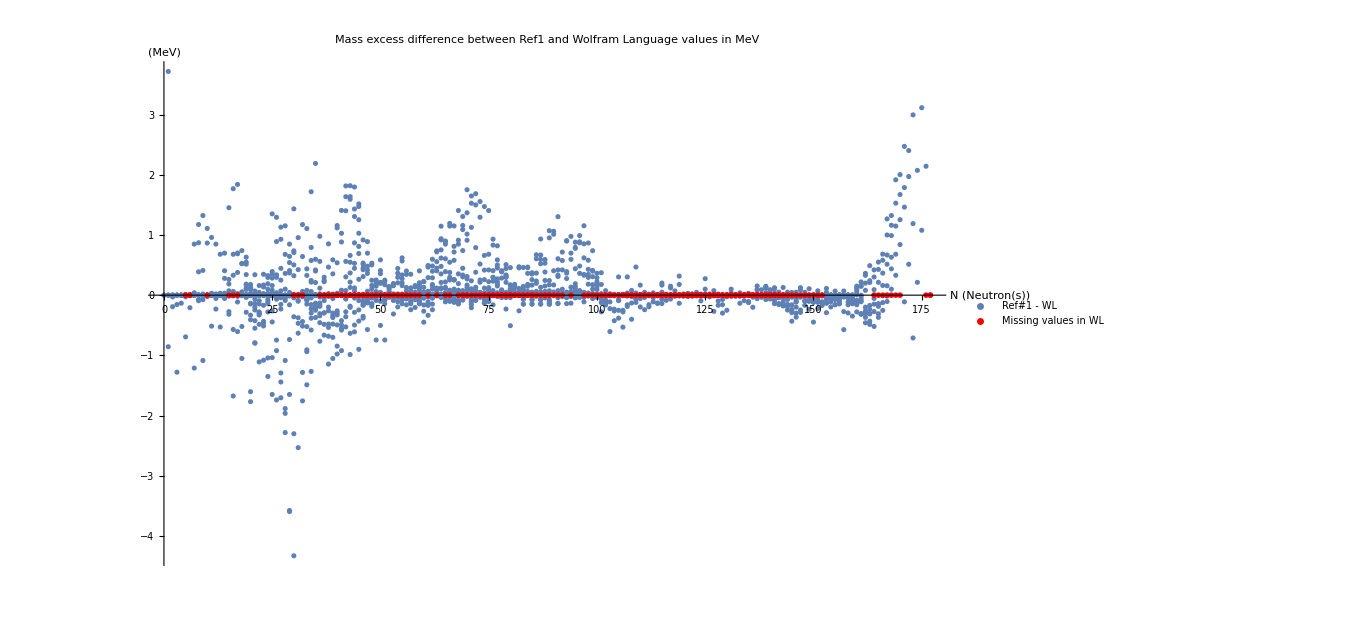

```mathematica
plotDifferenceBetweenMasses = ListPlot[{mathematicaData[[All,{2,5}]], listMissingElementsToPlot},
PlotRange->All,PlotStyle->{{},{Red,PointSize[0.004]}},
 AxesLabel->{"N (Neutron(s))","(MeV)"}, PlotLabel-> "Mass excess difference between Ref1 and Wolfram Language values in MeV",
PlotLegends-> {"Ref#1 - WL","Missing values in WL"},ImageSize-> 1000 ]
```

## Conclusion

I did this "mini-study" to compare the newest data in the area with the values provided by the Wolfram Language. One could see that WL needs to update their data.It is useful to play with it but it is not the good one to work with. I searched in their documentation and they say that the most recent data is from 2007. The data that I worked in this post is from 2016, the most recent one. The next data is expected to be released in 2022.

In conclusion, It would be great if WL has the most recent values to work with. I hope that you had enjoyed the notebook.
Thanks.